# Automatic Researcher

## Description

It’s 2021 and everyone tells you to do your own research. This is obviously absurd because doing research is hard and you’re not going to bother. This project will solve all of your problems by doing research automatically. You can then present a concise, coherent, and comprehensive breakdown of any subject at moment’s notice to win any argument without reading so much as a title. Now go forth and claim that sweet, sweet social credit!

## Basics

Start from keyword

Gather most relevant Wikipedia articles

Present summary

## Goal

Final product: cloud deployed web service

Input: keyword

Output: summary of relevant info and topics in readable form

Bonus: Link tree for important related topics/articles

## Plan

Start from Wikipedia article with title closest to given keyword

Trawl all links recursively to some (lowish) depth and form connectivity tree for topics

Take given number of most relevant articles

Summarize articles

Basic: take top section

Advanced: take sentences with most relevant keywords

After first sentence each major keyword is used, add in summary for relevant article

Continue recursively until depth or length limit is reached

Present information in readable form

## Testing

```mathematica
TextSentences[WikipediaData["research"]][[;;2]]
```

{Research is "creative and systematic work undertaken to increase the stock of knowledge".,It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.}

```mathematica
links=WikipediaData["Research","LinksRules","MaxLevel"->2,"MaxLevelItems"->5];
```

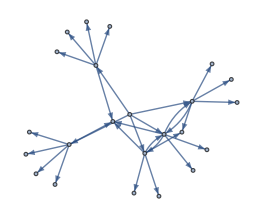

```mathematica
g=Graph[links,VertexLabels->Placed["Name",Tooltip]]
```

```mathematica
CommunityGraphPlot[g]
```

-Graphics-

```mathematica
f=?*Centrality*
```

```mathematica
(* show importance graph and list important articles for all built-in closeness measures *)
Column[Row[{Text@#,showImportance[g,#],o=getOrder[g,#];Column[o[[;;If[Length[o]>10,10,Length[o]]]]]}]&/@{
PageRankCentrality,EigenvectorCentrality,BetweennessCentrality,ClosenessCentrality,LinkRankCentrality,DegreeCentrality,EccentricityCentrality,EdgeBetweennessCentrality,HITSCentrality,KatzCentrality,RadialityCentrality,StatusCentrality
}]
(* pretty broken, PageRankCentrality seems best though *)
```

```mathematica
getLinks[article_,depth_,breadth_]:=WikipediaData[article,
	"LinksRules","MaxLevel"->depth,"MaxLevelItems"->5];
getLinksGraph[links_]:=Graph[links,VertexLabels->Placed["Name",Tooltip]]
showImportance[graph_,func_]:=HighlightGraph[graph,VertexList@graph,
	VertexSize->Thread[VertexList@graph->Rescale[func@graph]],ImageSize->Medium]
getOrder[graph_,func_]:=Part[VertexList[graph],Ordering[func[graph],All,Greater]]
getKeywords[graph_,n_]:=Take[o=getOrder[graph,PageRankCentrality],If[Length[o]>n,n,Length[o]]]
```

```mathematica
showImportance[g,PageRankCentrality]
```

-Graphics-

```mathematica
getOrder[g,PageRankCentrality]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal,Academic ghostwriting,Academic dishonesty,Academic discipline,Academic conference,APA style,Academic,ABC-CLIO,Academic rank,Academic personnel,Academic degree,Aalto University,Abolitionism in the United States,Abigail Thompson,2006 Duke University lacrosse case,14th Amendment to the U.S. Constitution,Academic ranks,Academic freedom,Research}

```mathematica
showImportance[g,EigenvectorCentrality]
```

-Graphics-

```mathematica
getOrder[g,EigenvectorCentrality]
```

{Academic authorship,Academic publishing,Academic journal,Academic rank,Academic personnel,Academic degree,Aalto University,Academic discipline,Academic conference,APA style,Academic,Abstract (summary),ABC-CLIO,Abolitionism in the United States,Abigail Thompson,2006 Duke University lacrosse case,14th Amendment to the U.S. Constitution,Academic ghostwriting,Academic dishonesty,Academia,Academic ranks,Academic freedom,Research}

```mathematica
links=getLinks["Research",2,10];
```

```mathematica
graph=getLinksGraph@links;
```

```mathematica
keywords=getKeywords[graph,5]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal}

```mathematica
fulltext=TextSentences[WikipediaData["Research"]];
```

```mathematica
Map[Function[keyword,keyword->Select[fulltext,StringContainsQ[#,keyword,IgnoreCase->True]&]],keywords]
```

{Academia→{In academia, scholarly peer review is often used to determine an academic paper's suitability for publication.},Academic authorship→{},Abstract (summary)→{},Academic publishing→{Academic publishing is a system that is necessary for academic scholars to peer review the work and make it available for a wider audience.},Academic journal→{The degree of originality of the research is among major criteria for articles to be published in academic journals and usually established by means of peer review.,As the great majority of mainstream academic journals are written in English, multilingual periphery scholars often must translate their work to be accepted to elite Western-dominated journals.,Most established academic fields have their own scientific journals and other outlets for publication, though many academic journals are somewhat interdisciplinary, and publish work from several distinct fields or subfields.}}

## Next

Look for pretrained networks in the Wolfram Neural Net Repository

Keyword extractor

Text summarizer

Text relationships

Correlate keywords with links

Find or build keyword choosing algorithm

Implement TextRank or adapt PageRankCentrality

Dynamically choose parameters for depth and breadth based on length requirement

Build recursion functions for full summaries

Hold link tree for navigation

Build web interface

```mathematica
links=getLinks["Research",2,10];
```

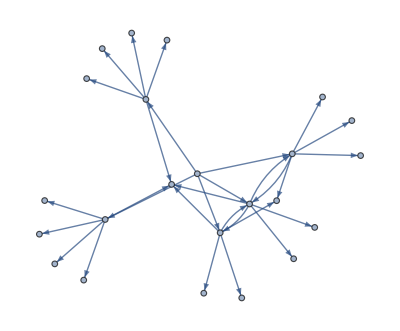

```mathematica
graph=getLinksGraph[links]
```

```mathematica
showImportance[graph,PageRankCentrality]
```

-Graphics-

```mathematica
getKeywords[graph,10]
```

{Academia,Academic authorship,Abstract (summary),Academic publishing,Academic journal,Academic ghostwriting,Academic dishonesty,Academic discipline,Academic conference,APA style}

## TextRank for Keyword Extraction

Filter only nouns and adjectives

Add lexical units to graph

Edge between units that co-occur within a window of N words

Run PageRankCentrality to find top keywords

Find important sentences

Option 1: sentences that contain most keywords

Option 2: run TextRank again for sentences instead

Output top sentences as summary

Find links related to top keywords

Recurse to add summaries

```mathematica
partialtext=fulltext[[1]]
```

Research is "creative and systematic work undertaken to increase the stock of knowledge".

```mathematica
cleanText[text_String]:=StringDelete[text,PunctuationCharacter]//ToLowerCase
```

```mathematica
filterWords[text_String]:=With[{pos=Association@@((#->WordData[#,"PartsOfSpeech"])&/@StringSplit[cleanText[text]])},
Select[Keys[pos],ContainsOnly[pos[#],{"Noun","Adjective"}]&]]
```

```mathematica
filterWords[partialtext]
```

{creative,systematic,collection,organization,analysis,information,understanding,topic,may,expansion,validity,procedures,elements,prior,primary,basic,opposed,applied,are,documentation,discovery,interpretation,development,methods,systems,advancement,human,knowledge}

```mathematica
partialtext=StringJoin[fulltext[[;;5]]]
```

Research is "creative and systematic work undertaken to increase the stock of knowledge".It involves the collection, organization, and analysis of information to increase understanding of a topic or issue.A research project may be an expansion on past work in the field.To test the validity of instruments, procedures, or experiments, research may replicate elements of prior projects or the project as a whole.The primary purposes of basic research (as opposed to applied research) are documentation, discovery, interpretation, and the research and development (R&D) of methods and systems for the advancement of human knowledge.

```mathematica
keywords=filterWords[partialtext]
```

{creative,systematic,collection,organization,analysis,information,understanding,topic,may,expansion,validity,procedures,elements,prior,primary,basic,opposed,applied,are,documentation,discovery,interpretation,development,methods,systems,advancement,human,knowledge}

```mathematica
nextWords[text_,word_,n_]:=With[{words=StringSplit[cleanText[text]],i=Position[words,word][[1,1]]},Take[Rest[words][[i;;UpTo[i+n]]]]]
```

```mathematica
cleanWords=StringSplit@cleanText@partialtext
```

{research,is,creative,and,systematic,work,undertaken,to,increase,the,stock,of,knowledgeit,involves,the,collection,organization,and,analysis,of,information,to,increase,understanding,of,a,topic,or,issue}

```mathematica
Position[cleanWords,"to"]
```

{{8},{22}}

```mathematica
cleanWords[[{1}]]
```

{research}

```mathematica
cleanWords[[{1,2}]]
```

{research,is}

```mathematica
Position[textwords,"project"]
```

{{31},{59}}

```mathematica
textwords=StringSplit[cleanText[partialtext]]
```

{research,is,creative,and,systematic,work,undertaken,to,increase,the,stock,of,knowledgeit,involves,the,collection,organization,and,analysis,of,information,to,increase,understanding,of,a,topic,or,issuea,research,project,may,be,an,expansion,on,past,work,in,the,fieldto,test,the,validity,of,instruments,procedures,or,experiments,research,may,replicate,elements,of,prior,projects,or,the,project,as,a,wholethe,primary,purposes,of,basic,research,as,opposed,to,applied,research,are,documentation,discovery,interpretation,and,the,research,and,development,rd,of,methods,and,systems,for,the,advancement,of,human,knowledge}

```mathematica
Partition[textwords,Min[Length[textwords],5]]
```

{{research,is,creative,and,systematic},{work,undertaken,to,increase,the},{stock,of,knowledgeit,involves,the},{collection,organization,and,analysis,of},{information,to,increase,understanding,of},{a,topic,or,issuea,research},{project,may,be,an,expansion},{on,past,work,in,the},{fieldto,test,the,validity,of},{instruments,procedures,or,experiments,research},{may,replicate,elements,of,prior},{projects,or,the,project,as},{a,wholethe,primary,purposes,of},{basic,research,as,opposed,to},{applied,research,are,documentation,discovery},{interpretation,and,the,research,and},{development,rd,of,methods,and},{systems,for,the,advancement,of}}

```mathematica
wordlist=First@%175
```

{research,is,creative,and,systematic}

```mathematica
linkAllKeywords[wordlist_,keywords_]:=Flatten[Function[word,If[MemberQ[keywords,#]&&word!=#,word->#,Nothing]&/@wordlist]/@Select[wordlist,MemberQ[keywords,#]&]]
```

```mathematica
localKeywordLinks[wordlist_,keywords_,distance_]:=
Flatten[linkAllKeywords[#,keywords]&/@Partition[wordlist,Min[Length[wordlist],distance]]]//Function[DeleteCases[#,{}]]
```

```mathematica
localKeywordLinks[textwords,keywords,5]
```

{}

```mathematica
keywords=WikipediaData["Research","LinksList"]
```

## Revised Method

Get Article Summary:

Find most important keywords using PageRankCentrality of all article links

Find most important sentences using PageRankCentrality of sentence relations

For each important sentence that contains an important link, splice in article summary of link

Recursively combine article summaries down to given level

## Get Important Sentences

```mathematica
sentenceSimilarity[s1_,s2_]:=With[{c1=getWords[s1],c2=getWords[s2]},
Length[Intersection[c1,c2]]/(Log[Length[c1]]+Log[Length[c2]])]//N
```